```mathematica
(*Make the whole script depend on the increase in performance @ 75% correct*)
```

Criterion as discussed in our Zoom call (04.03.2026) was that at 75% correct we require an increase of 2% in prediction performance to be a “meaningful” effect size, i.e. an increase in predictability we argue is worth increasing the dimensionality for.

Three possible approaches:
1. SDT
Assume an unbiased YesNo observer with n = N(0,1) and s = N(d’, 1); optimal performance with equally likely signal and noise trials for criterion lambda = 0.5*d’. Calculate the increase in d’ necessary to achieve a certain performance gain at a reference performance, i.e. 2% at 75%.

2. LogOdds
In terms of LogOdds: For a given performance p we have the LogOdds = log(p/(1-p)).  this means we require a Δ such that Log[0.75/0.25]+ Δ = Log[0.77/0.23]. 

3. We argue that we want to know a constant fraction of what is “remaining”: If a decision-maker is at performance p, there is 1-p left to improve. We want a constant fraction of this before we say we found a meaningful effect size, e.g. 5 or 10% of 1-p.

```mathematica
(* Choose starting point in terms of p and the delta in improvement*)
myP = 0.75; myDelta = 0.02;
```

```mathematica
(* Translate the above condition into a dPrimeOffset *)
dPrime=InverseCDF[NormalDistribution[0,1], myP]-InverseCDF[NormalDistribution[0,1], 1-myP];
dPrimeD=InverseCDF[NormalDistribution[0,1], myP+myDelta]-InverseCDF[NormalDistribution[0,1], 1-myP-myDelta];
dPrimeOffset = dPrimeD - dPrime
```

0.128714

```mathematica
(* Translate the above condition into a logOddsOffset*)
logOddsOffset = N[Log[(myP+myDelta)/(1-myP-myDelta)]-Log[myP/(1-myP)]]
```

0.109699

```mathematica
(* Translate the above condtion into a constant fraction of resolved *)
```

```mathematica
fractionOffset = myDelta/(1-myP)
```

0.08

```mathematica
(* Calculate d' for the optimal YesNo observer as a function of percent correct*)
```

```mathematica
dP[x_]:= InverseCDF[NormalDistribution[0,1], x]-InverseCDF[NormalDistribution[0,1], 1-x]
```

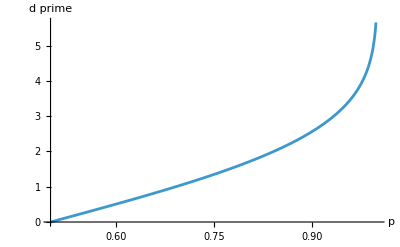

```mathematica
Plot[dP[x], {x, 0.5, 1}, AxesLabel->{"p","d prime"}]
```

```mathematica
(* Calculate percent correct from d' *)
pC[x_]:=1 - CDF[NormalDistribution[x,1], x/2]
```

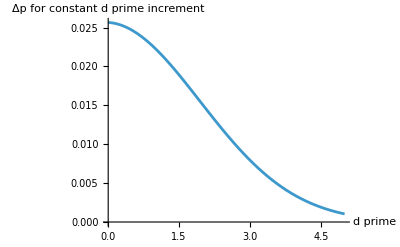

```mathematica
Plot[pC[x+dPrimeOffset]-pC[x], {x, 0, 5}, AxesLabel->{"d prime","Δp for constant d prime increment"}]
```

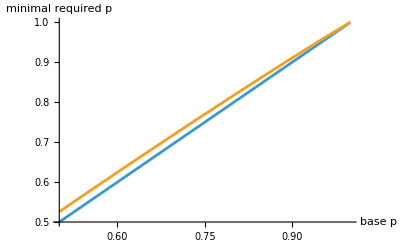

```mathematica
Plot[{pC[dP[p]],pC[dP[p]+ dPrimeOffset]}, {p, 0.5, 1}, AxesLabel->{"base p", "minimal required p" }]
```

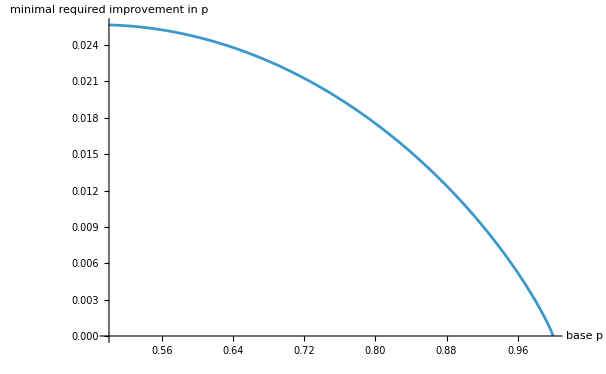

```mathematica
Plot[pC[dP[p]+ dPrimeOffset]-pC[dP[p]], {p, 0.5, 1}, AxesLabel->{"base p", "minimal required improvement in p" }]
```

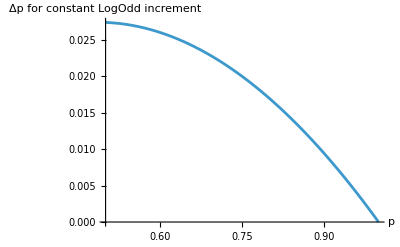

```mathematica
(* Clear alpha *)
Clear[α]

(* Solve the equation *)
solution=Solve[Log[p/(1-p)]+α==Log[(p+Δ)/(1-(p+Δ))],Δ];

(* Extract the expression for Δ *)
deltaExpr=Δ /. solution;

(* Plot the expression for Δ as a function of p *)
Plot[Evaluate[deltaExpr /. α->logOddsOffset],{p,0.5,1},AxesLabel->{"p","Δp for constant LogOdd increment"}]
```

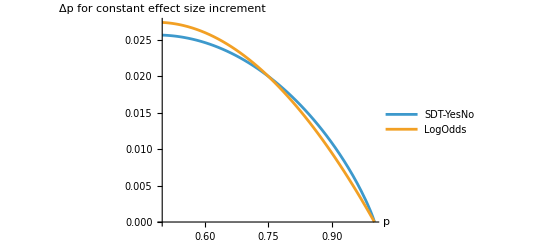

```mathematica
Plot[{pC[dP[p]+ dPrimeOffset]-pC[dP[p]],Evaluate[deltaExpr /. α-> logOddsOffset]},{p,0.5,1},AxesLabel->{"p","Δp for constant effect size increment"}, PlotLegends->{"SDT-YesNo", "LogOdds"}]
```

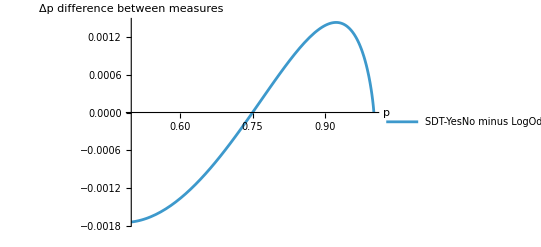

```mathematica
Plot[(pC[dP[p]+ dPrimeOffset]-pC[dP[p]])- Evaluate[deltaExpr /. α->logOddsOffset],{p,0.5,1},AxesLabel->{"p","Δp difference between measures"}, PlotLegends->{"SDT-YesNo minus LogOdds"}]
```

```mathematica
Solve[(Log[p/(1-p)]+ α) == Log[(p+Δ)/(1-(p+Δ))], Δ]
```

{{Δ→ConditionalExpression[(-p+(ⅇ^α p)/(1-p)-(ⅇ^α p^2)/(1-p))/(1+(ⅇ^α p)/(1-p)), -π<Im[α+Log[p/(1-p)]]≤π]}}